# The Sandpile Model

Jonas Kaufman & Jon Ueki

## Introduction

The Sandpile Model, also known as the Bak-Tang-Wiesenfeld model, is a cellular automaton that aims to model...

## Graphics Setup

```mathematica
Module[{cmds= {"Plot", "ListPlot", "ListLinePlot", "ListLogPlot", "ListLogLogPlot","LogPlot","LogLogPlot","ListStepPlot"}},
For[j=1, j≤ Length[cmds],j++,SetOptions[Symbol[ cmds[[j]] ], Frame->True,LabelStyle->{Larger, FontFamily->"Utopia"}]]
]
```

## 1-D Model

The model takes place on a row representing half a sandpile where each cell has a slope z_n and height h_n where z_n=h_n-h_(n+1)......

### Initialization

The global variable row keeps track of the slope at each cell

```mathematica
length=20; (* length of row *)
zCrit1D=1;(* critical slope *)
randomRow[]:=row=Table[RandomInteger[zCrit],{length}] (* initialize row randomly *)
constantRow[c_]:=row=Table[c,{length}](* initialize row to constant slope *)
```

### Updating

relaxation1D relaxes the entire row until stable

```mathematica
relaxation1D[]:=Module[{i,stable=False},
While[!stable,
stable=True;
For[i=1,i≤ length,i++,
If[row[[i]]> zCrit1D,
stable=False;
If[1<i<length,row[[i]]-=2;row[[i+1]]++;row[[i-1]]++;];
If[i==1,row[[i]]-=2;row[[i+1]]++;];
If[i==length,row[[i]]--;row[[i-1]]++];
];
];
];
]
```

addGrain adds a grain of sand at a specific or random place

```mathematica
addGrain1D[] :=Module[{r},
r=RandomInteger[{1,length}];
row[[r]]++;
If[r>1,row[[r-1]]--]
];
```

pourSand adds numGrains grains of sand and relaxes after each

```mathematica
pourSand[numGrains_]:=Module[{n,rows={row}},
For[n=1,n≤numGrains,n++,
addGrain1D[];
relaxation1D[];
AppendTo[rows,row]; 
];
rows
]
```

### Simulation

If sand is added randomly to an empty row, the pile eventually reaches a critical state in which the slope at each cell is simply the critical slope.

```mathematica
constantRow[0];
rows=pourSand[600];
Animate[GraphicsColumn[{
ListStepPlot[Table[Total[rows[[t]][[i;;]]],{i,length}],FrameLabel->{"i","h"},PlotRange->{0,length*zCrit1D+1}],
ListStepPlot[rows[[t]],FrameLabel->{"i","z"},PlotRange->{-zCrit1D-1,zCrit1D+1}]
}],{t,1,Length[rows],1,Appearance->"Labeled"},AnimationRunning->False,AnimationRate->Automatic]
```

## 2-D Model

The model takes place on a grid...

#### Initialization

The global variable grid keeps track of the slope at each cell

```mathematica
gridSize = 20; (* side length of grid *)
zCrit = 2; (* the critical slope *)
randomGrid[]:=grid = Table[Table[RandomInteger[zCrit], {n, gridSize}], {n, gridSize}]; (* initialize grid randomly *)
constantGrid[c_]:=grid = Table[Table[c, {n, gridSize}], {n, gridSize}]; (* initialize grid to constant slope *)
```

#### Updating

relaxAll relaxes the entire grid until stable

```mathematica
relaxAll[]:=Module[{i,j,stable=False},
While[!stable,
stable=True;
For[i=1,i≤ gridSize,i++,
For[j=1,j≤ gridSize,j++,
If[grid[[i,j]]> zCrit,
stable=False;
(* remove slope *)
grid[[i,j]]-=2;
If[i≠ gridSize,grid[[i,j]]--];
If[j≠ gridSize,grid[[i,j]]--];
(* add slope to neighbors *)
If[i≠1,grid[[i-1,j]]++];
If[j≠1,grid[[i,j-1]]++];
If[i≠gridSize,grid[[i+1,j]]++];
If[j≠gridSize,grid[[i,j+1]]++];
];
];
];
];
]
```

update relaxes a single cell and it’s neighbors (then their neighbors, etc.) until stable

```mathematica
update[ii_,jj_]:=Module[{stable=False,look={{ii,jj}},l,i,j},
While[!stable,
stable=True;
For[l=1,l≤ Length[look],l++,
{i,j}=look[[l]];
If[grid[[i,j]]>zCrit,
stable=False;
s++; (* count topple *)
(* remove slope *)
grid[[i,j]]-=2;
If[i≠ gridSize,grid[[i,j]]--];
If[j≠ gridSize,grid[[i,j]]--];
(* add slope to neighbors *)
If[i≠1,grid[[i-1,j]]++];
If[j≠1,grid[[i,j-1]]++];
If[i≠gridSize,grid[[i+1,j]]++];
If[j≠gridSize,grid[[i,j+1]]++];
(* relax neighbors *)
If[i≠1,AppendTo[look,{i-1,j}]];
If[j≠1,AppendTo[look,{i,j-1}]];
If[i≠gridSize,AppendTo[look,{i+1,j}]];
If[j≠gridSize,AppendTo[look,{i,j+1}]];
];
];
];
]
```

addSand adds a grain of sand at a specific or random place

```mathematica
addGrain[random_,place_] :=Module[{i, j}, 
If[random,(*If we activate random, then add grains randomly*)
i=RandomInteger[{1,gridSize}];j=RandomInteger[{1,gridSize}];,
i=place[[1]];j=place[[2]];
];
grid[[i,j]]+=2;
If[j≠1,grid[[i,j-1]]--];
If[i≠1,grid[[i-1,j]]--];
update[i,j];
]
```

run adds totalSand_ grains of sand and relaxes after each
returns a list of the total number of topples each time step

```mathematica
run[totalSand_, random_:False,place_:{1,1}] := Module[{n,T,sList={},TList={}},
For[n=1,n≤ totalSand,n++,
s=0;
addGrain[random,place];
AppendTo[sList,s];
];
{grid,sList}
]
```

#### Statistics

Distribution of slopes

```mathematica
slopeDist[]:= Module[{slopes, negslopes, slopedist = {}, i, j},
slopes = Table[0, {n, 0, zCrit+1}];
negslopes = Table[0, {n, 0, zCrit*5}];
For[i=1, i≤ gridSize, i++,
For[j=1, j≤gridSize,j++,
If[grid[[i,j]]<0,
negslopes[[Abs[grid[[i,j]]]]]++, 
slopes[[grid[[i,j]] + 1]]++;
];
];
];
(*make x-coordinate and y-coordinate pair *)
For[i=1, i≤Length[slopes], i++,
AppendTo[slopedist, {i-1,1./gridSize^2 slopes[[i]]}];
];
For[i=1, i≤Length[negslopes], i++,
AppendTo[slopedist, {-1 * i, 1./gridSize^2 negslopes[[i]]}];
];
 slopedist
]
```

sDist produces a distribution of avalanche sizes from a list of avalanche sizes at each time step

```mathematica
sDist[sList_]:=Module[{dist=Table[0,{Max[sList]}],s,t},
For[t=1,t≤ Length[sList],t++,
s=sList[[t]];
If[s≠0,
dist[[s]]++
];
];
1./Length[sList] dist
]
```

#### Visualization

heights calculates an array of heights based on an array of slopes

```mathematica
heights[grid_]:=Module[{i,j,gridSize=Length[grid],heights},
heights=Table[Table[0, {gridSize}], {gridSize}];
For[i=gridSize-1,i> 0,i--,
For[j=gridSize-1,j> 0,j--,
heights[[i,j]]= 0.5(grid[[i,j]]+heights[[i+1,j]]+heights[[i,j+1]]);
];
];
heights
]
```

heightFull calculates an array of heights for the full sandpile based on one quarter of it

```mathematica
heightsFull[grid_]:=Module[{i,j,h,gridSize=Length[grid],heights},
heights=Table[Table[0, {n, 2*gridSize}], {n, 2*gridSize}];
For[i=gridSize-1,i≥0,i--,
For[j=gridSize-1,j≥0,j--,
h=0.5(If[i==0 || j==0,grid[[i+1,j+1]] ,grid[[i,j]]]
+ heights[[i+1 + gridSize,j + gridSize]]
+heights[[i + gridSize,j+1 + gridSize]]);
heights[[gridSize+i,gridSize+j]]=h;
heights[[gridSize+i, gridSize - j]] =h;
heights[[gridSize-i, gridSize+j]] = h;
heights[[gridSize-i, gridSize - j]] = h;
];
];
heights
]
```

#### Run and Plot the Simulation

```mathematica
constantGrid[4];
```

```mathematica
relaxAll[];
```

```mathematica
sList=run[10000, True];
```

```mathematica
Dynamic[GraphicsRow[{ArrayPlot[grid,PlotLegends->Automatic,ColorFunction->GrayLevel],
ArrayPlot[heights[grid],PlotLegends->Automatic,ColorFunction->GrayLevel]},
ImageSize->Large,AspectRatio->3/4]]
```

```mathematica
ArrayPlot[grid,PlotLegends->Automatic,ColorFunction->GrayLevel,PlotLabel->z]
```

-Graphics-

```mathematica
ArrayPlot[heights[grid],PlotLegends->Automatic,ColorFunction->GrayLevel,PlotLabel->h]
```

-Graphics-

```mathematica
ListPlot3D[heightsFull[grid],InterpolationOrder->1, Mesh->None,ColorFunction->"Rainbow"]
```

-Graphics3D-

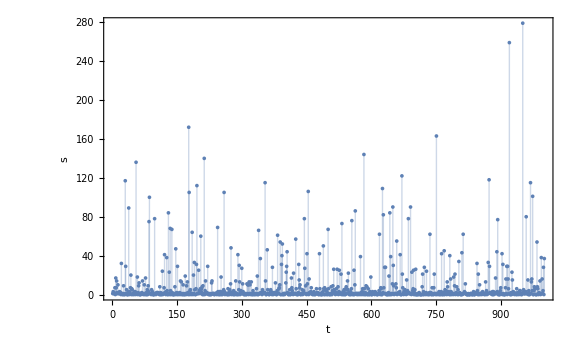

```mathematica
ListPlot[sList[[99000;;]],PlotRange->All,Filling->Axis,FrameLabel->{t,"s"},ImageSize->Large,LabelStyle->Large]
```

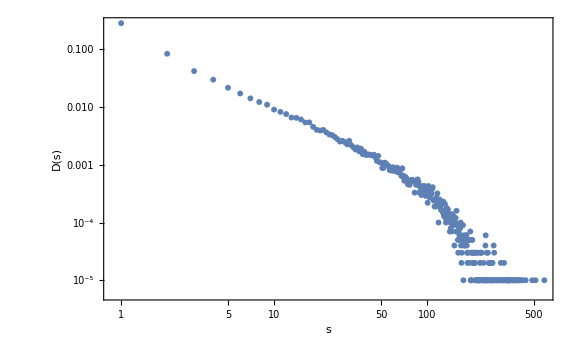

```mathematica
ListLogLogPlot[sDist[sList],FrameLabel->{"s","D(s)"},ImageSize->Large,LabelStyle->Large]
```

```mathematica
FindFit[sDist[sList],a*x^b,{a,b},x]
```

{a→0.283114,b→-1.63411}

#### N=20, Zc=3, Random=False, Zi=0, 100k steps

```mathematica
constantGrid[0];
```

```mathematica
sList1=run[10000];
```

```mathematica
slopeDist1 = slopeDist[]
```

(0 | 0.1825
1 | 0.285
2 | 0.4675
3 | 0.
-1 | 0.065
-2 | 0.
-3 | 0.
-4 | 0.
-5 | 0.
-6 | 0.
-7 | 0.
-8 | 0.
-9 | 0.
-10 | 0.
-11 | 0.)

```mathematica
ListPlot3D[heightsFull[grid],InterpolationOrder->1, Mesh->None,ColorFunction->"Rainbow"]
```

-Graphics3D-

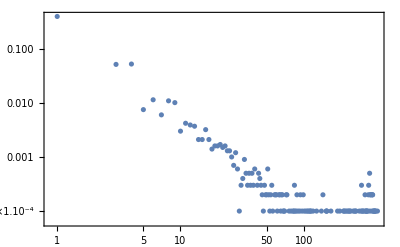

```mathematica
ListLogLogPlot[sDist[sList1]]
```

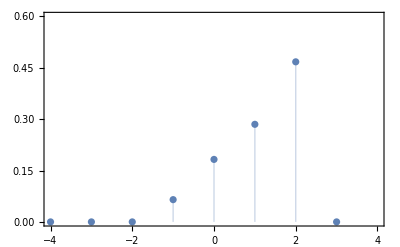

```mathematica
ListPlot[slopeDist1, Filling->Axis, PlotRange-> {{-4,4}, {0,.6}}]
```

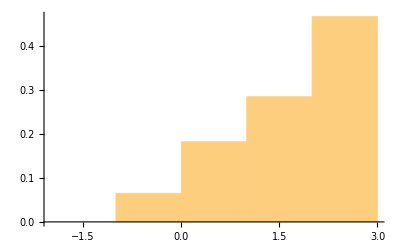

```mathematica
Histogram[Flatten[grid],Automatic,"Probability"]
```

#### N=20, Zc=3, Random=True, Zi=0, 100k steps

```mathematica
constantGrid[0];
```

```mathematica
sList2=run[100000, True];
```

```mathematica
slopeDist2 = slopeDist[];
```

```mathematica
ListPlot3D[heightsFull[grid],InterpolationOrder->1, Mesh->None,ColorFunction->"Rainbow"]
```

-Graphics3D-

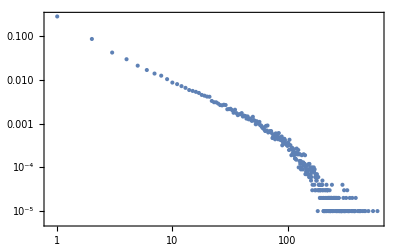

```mathematica
ListLogLogPlot[sDist[sList2]]
```

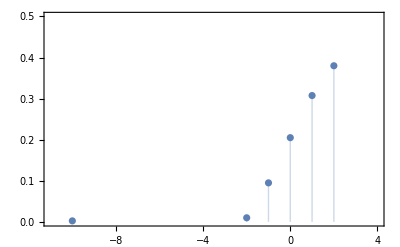

```mathematica
ListPlot[slopeDist2, Filling->Axis, PlotRange-> {{-11,4}, {0,.5}}]
```

#### N=20, Zc=3, Zi=9, Random=True, 100k

```mathematica
constantGrid[4];
```

The before Picture

```mathematica
ListPlot3D[heightsFull[grid],InterpolationOrder->1, Mesh->None,ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
relaxAll[];
```

```mathematica
slopeDist3 = slopeDist[];
```

The after picture

```mathematica
ListPlot3D[heightsFull[grid],InterpolationOrder->1, Mesh->None,ColorFunction->"Rainbow"]
```

-Graphics3D-

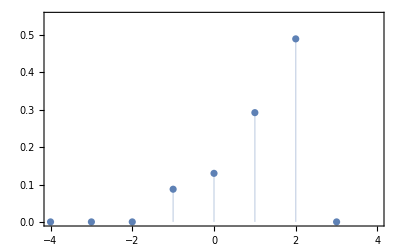

```mathematica
ListPlot[slopeDist3, Filling->Axis, PlotRange-> {{-4,4}, {0,.55}}]
```

Now perturb the state by adding 100k sand grains

```mathematica
sList3 = run[100000,True]
```

{1,1,2,17,2,175,49,32,67,1,14,1,20,75,0,1,224,8,0,3,2,1,3,1,0,59,2,0,4,0,0,51,0,1,2,100,13,33,0,0,1,0,0,54,1,12,11,1,1,98,0,1,10,0,2,2,33,5,1,0,9,0,0,27,2,0,2,1,0,1,72,38,2,245,9,1,2,0,0,25,55,92,1,0,2,1,0,87,0,6,0,44,0,0,73,1,2,1,229,8,1,5,1,2,0,2,2,7,17,1,201,5,40,1,2,1,1,0,0,1,0,0,16,99755,0,9,0,0,0,1,0,42,1,3,2,26,10,0,1,1,1,7,32,0,0,0,0,1,0,141,0,1,0,1,1,0,5,1,1,0,0,1,79,3,9,6,1,0,0,5,0,1,0,1,11,38,3,10,1,1,41,8,1,0,0,1,122,0,0,0,0,9,0,89,1,0,0,5,0,94,0,1,9,36,0,2,31,6,0,1,5,2,1,72,2,0,0,1,7,1,0,1,0,1,0,11,2,0,28,1,20,6,2,10,3,0,0,1,3,1,2,1,1,13,0,1}
 |  |  |  |

```mathematica
ListPlot3D[heightsFull[grid],InterpolationOrder->1, Mesh->None,ColorFunction->"Rainbow"]
```

-Graphics3D-

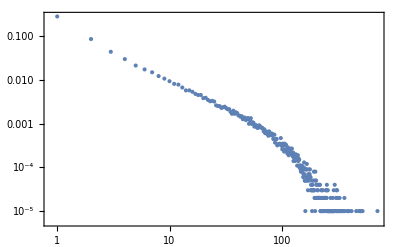

```mathematica
ListLogLogPlot[sDist[sList3]]
```

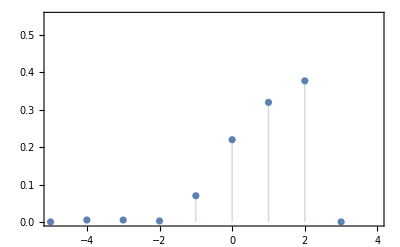

```mathematica
ListPlot[slopeDist[], Filling->Axis, PlotRange-> {{-5,4}, {0,.55}}]
```

#### N=20, Zc=3, Zi=9, Random=False, 100k

```mathematica
constantGrid[9];
```

```mathematica
relaxAll[];
```

```mathematica
sList4 = run[100000]
```

{4,1,0,1,0,59,1,0,3,1,0,1,0,1,0,40,1,0,12,1,0,4,1,0,1,0,3,1,0,1,0,1,0,23,1,0,9,1,0,1,0,8,1,0,4,1,0,1,0,3,1,0,1,0,1,0,6,1,0,3,1,0,1,0,1,0,7,1,0,1,0,8,1,0,3,1,0,1,0,1,0,29,1,0,6,1,0,1,0,4,1,0,1,0,24,1,0,3,1,0,1,0,1,0,6,1,0,3,1,0,1,0,1,0,12,1,0,1,0,11,1,0,4,1,0,1,0,5,1,0,1,0,11,1,99732,1,0,8,1,0,4,1,0,1,0,3,1,0,1,0,1,0,4,1,0,1,0,15,1,0,3,1,0,1,0,1,0,11,1,0,4,1,0,1,0,3,1,0,1,0,1,0,10,1,0,4,1,0,1,0,3,1,0,1,0,1,0,121,1,0,55,1,0,4,1,0,1,0,3,1,0,1,0,1,0,9,1,0,4,1,0,1,0,3,1,0,1,0,1,0,45,1,0,50,1,0,1,0,25,1,0,4,1,0,1,0,8,1,0,3,1,0,1,0,1,0,4,1,0,1,0,5,1,0,1,0,35,1,0}
 |  |  |  |